```mathematica
Quiet[Remove["Global`*"]];
ass[a_,x0_,y0_, k1_, k2_,x1_,x2_,y1_,y2_] := {x0∈Reals&&y0∈Reals&&a>0&&k1>0&&k2>0&&x1∈Reals&&x2∈Reals&&x2>x1&&y1∈Reals&&y2∈Reals&&y2>y1};
g[y_,m_, s2_]:=Exp[-(y-m)^2/2/s2];
r[a_,x_, y_, x0_, y0_, k_]:=g[y, y0+k*(x-x0), ((y0+k*(x-x0))*a)^2];
(*z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_] :=Integrate[r[a,x,y,x0,y0,k],{x,x1,x2},{y,y1,y2}];*)
z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_]:=Integrate[a √(π/2) (k (x-x0)+y0) *(Erf[(k (x-x0)+y0-y1)/(√2 a (k (x-x0)+y0))]-Erf[(k (x-x0)+y0-y2)/(√2 a (k (x-x0)+y0))]),{x,x1,x2},Assumptions->ass[a,x0,y0, k, k,x1,x2,y1,y2]];
s[a_,x0_,y0_, k1_, k2_,x1_,x2_,y1_,y2_] := Integrate[r[a,x,y,x0,y0,Min[k1,k2]],{x,x1,x2},{y,y0+(k1+k2)/2*(x-x0),y2},Assumptions->ass[a,x0,y0, k1, k2,x1,x2,y1,y2]]/z[a,x0,y0,k1,x1,x2,y1,y2] + Integrate[r[a,x,y,x0,y0,Max[k1,k2]],{x,x1,x2},{y,y1,y0+(k1+k2)/2*(x-x0)},Assumptions->ass[a,x0,y0, k1, k2,x1,x2,y1,y2]]/z[a,x0,y0,k2,x1,x2,y1,y2];
```

```mathematica
z[a,x0,y0,k2,x1,x2,y1,y2]
```

```mathematica
s[a,x0,y0, k1, k2,x1,x2,y1,y2]
```

$Aborted

```mathematica
Quiet[Remove["Global`*"]];

g[y_,m_,s2_]:=Exp[-(y-m)^2/2/s2];
r[a_,x_, y_, x0_, y0_, k_]:=g[y, y0+k*(x-x0), ((y0+k*(x-x0))*a)^2];
(*z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_] :=Integrate[r[a,x,y,x0,y0,k],{x,x1,x2},{y,y1,y2}];*)
z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_]:=NIntegrate[a √(π/2) (k (x-x0)+y0) *(Erf[(k (x-x0)+y0-y1)/(√2 a (k (x-x0)+y0))]-Erf[(k (x-x0)+y0-y2)/(√2 a (k (x-x0)+y0))]),{x,x1,x2}];
s[a_,x0_,y0_, k1_, k2_,x1_,x2_,y1_,y2_] := 1-(NIntegrate[r[a,x,y,x0,y0,Min[k1,k2]]*UnitStep[y-(y0+(k1+k2)/2*(x-x0))],{x,x1,x2},{y,y1,y2}]/z[a,x0,y0,k1,x1,x2,y1,y2] + NIntegrate[r[a,x,y,x0,y0,Max[k1,k2]]*UnitStep[(y0+(k1+k2)/2*(x-x0))-y],{x,x1,x2},{y,y1,y2}]/z[a,x0,y0,k2,x1,x2,y1,y2]);
```

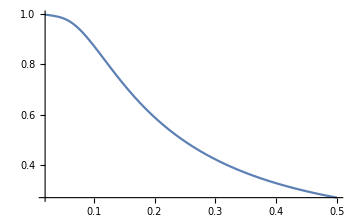

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.997892,0.997632,0.997362,0.997081,0.99679,0.996487,0.996173,0.995849,0.995513,0.995165,0.994805,0.994432,0.994046,0.993646,0.99323,0.992799,0.99235,0.991883,0.991395,0.990886,0.990352,0.989793,0.989207,0.98859,0.987941,0.987258,0.986538,0.985779,0.984978,0.984135,0.983246,0.98231,0.981324,0.980288,0.9792,0.978058,0.976861,0.975609,0.974301,0.972935,0.971512,0.970031,0.968492,0.966895,0.96524,0.963527,0.961757,0.95993,0.958048,0.956109,0.954116,0.952069,0.949969,0.947817,0.945615,0.943362,0.941062,0.938713,0.936319,0.93388,0.931398,0.928873,0.926307,0.923702,0.921059,0.91838,0.915665,0.912916,0.910134,0.907322,0.904479,0.901608,0.89871,0.895787,0.892839,0.889867,0.886874,0.88386,0.880827,0.877776,0.874707,0.871623,0.868524,0.865412,0.862287,0.859151,0.856004,0.852848,0.849684,0.846513,0.843335,0.840151,0.836963,0.833771,0.830576,0.827379,0.82418,0.820981,0.817782,0.814584,0.811387,0.808193,0.805001,0.801813,0.798629,0.795449,0.792274,0.789105,0.785942,0.782786,0.779636,0.776495,0.773361,0.770235,0.767118,0.764011,0.760912,0.757824,0.754746,0.751678,0.748621,0.745575,0.74254,0.739516,0.736505,0.733505,0.730517,0.727542,0.72458,0.72163,0.718693,0.71577,0.712859,0.709962,0.707078,0.704208,0.701352,0.698509,0.695681,0.692866,0.690066,0.687279,0.684507,0.681749,0.679006,0.676276,0.673562,0.670861,0.668175,0.665504,0.662847,0.660204,0.657577,0.654963,0.652364,0.64978,0.64721,0.644655,0.642114,0.639587,0.637075,0.634578,0.632095,0.629626,0.627171,0.624731,0.622305,0.619893,0.617495,0.615111,0.612742,0.610386,0.608045,0.605717,0.603403,0.601103,0.598816,0.596543,0.594284,0.592038,0.589806,0.587587,0.585382,0.58319,0.581011,0.578845,0.576692,0.574552,0.572425,0.570311,0.56821,0.566121,0.564045,0.561982,0.559931,0.557893,0.555867,0.553853,0.551851,0.549861,0.547884,0.545918,0.543965,0.542023,0.540093,0.538174,0.536268,0.534372,0.532488,0.530616,0.528755,0.526905,0.525066,0.523238,0.521422,0.519616,0.517821,0.516037,0.514263,0.512501,0.510748,0.509007,0.507276,0.505555,0.503844,0.502144,0.500453,0.498773,0.497103,0.495443,0.493792,0.492152,0.490521,0.4889,0.487288,0.485686,0.484094,0.482511,0.480937,0.479373,0.477817,0.476271,0.474734,0.473206,0.471687,0.470177,0.468676,0.467182,0.4657,0.464224,0.462758,0.4613,0.45985,0.458409,0.456977,0.455552,0.454136,0.452728,0.451328,0.449937,0.448553,0.447177,0.445809,0.444449,0.443097,0.441753,0.440416,0.439087,0.437766,0.436452,0.435145,0.433847,0.432555,0.431271,0.429994,0.428724,0.427462,0.426207,0.424958,0.423717,0.422483,0.421256,0.420036,0.418822,0.417616,0.416416,0.415223,0.414036,0.412856,0.411683,0.410517,0.409357,0.408203,0.407056,0.405915,0.40478,0.403652,0.40253,0.401414,0.400305,0.399201,0.398104,0.397012,0.395927,0.394847,0.393774,0.392706,0.391645,0.390589,0.389539,0.388494,0.387455,0.386422,0.385395,0.384373,0.383357,0.382346,0.38134,0.380341,0.379346,0.378357,0.377373,0.376395,0.375421,0.374453,0.37349,0.372533,0.37158,0.370633,0.36969,0.368753,0.36782,0.366893,0.365971,0.365053,0.36414,0.363232,0.362329,0.361431,0.360537,0.359648,0.358764,0.357884,0.357009,0.356139,0.355273,0.354412,0.353555,0.352703,0.351855,0.351011,0.350172,0.349338,0.348507,0.347681,0.346859,0.346042,0.345228,0.344419,0.343614,0.342813,0.342016,0.341223,0.340435,0.33965,0.338869,0.338093,0.33732,0.336551,0.335786,0.335025,0.334268,0.333515,0.332765,0.332019,0.331277,0.330539,0.329804,0.329073,0.328346,0.327622,0.326902,0.326186,0.325473,0.324764,0.324058,0.323355,0.322657,0.321961,0.321269,0.320581,0.319895,0.319213,0.318535,0.31786,0.317188,0.316519,0.315854,0.315191,0.314533,0.313877,0.313224,0.312575,0.311929,0.311285,0.310645,0.310008,0.309374,0.308743,0.308116,0.307491,0.306869,0.30625,0.305634,0.305021,0.304411,0.303803,0.303199,0.302597,0.301998,0.301402,0.300809,0.300219,0.299631,0.299045,0.298463,0.297884,0.297307,0.296733,0.296161,0.295593,0.295026,0.294463,0.293902,0.293343,0.292787,0.292234,0.291683,0.291135,0.290589,0.290046,0.289505,0.288966,0.28843,0.287897,0.287366,0.286837,0.286311,0.285786,0.285265,0.284745,0.284228,0.283714,0.283201,0.282691,0.282183,0.281677,0.281174,0.280672,0.280174,0.279677,0.279182,0.27869,0.278199,0.277711,0.277225,0.27674,0.276259,0.275779,0.275301,0.274825,0.274351,0.27388,0.27341,0.272942,0.272477,0.272013,0.271551,0.271091,0.270633,0.270178,0.269724,0.269272,0.268821,0.268373,0.267927,0.267482,0.267039,0.266599,0.26616,0.265722,0.265287,0.264853,0.264421,0.263991,0.263563,0.263137,0.262712,0.262289,0.261867,0.261448,0.26103,0.260614,0.260199,0.259786,0.259375,0.258966,0.258558,0.258151,0.257747,0.257344,0.256942,0.256542,0.256144,0.255747,0.255352,0.254959,0.254567,0.254176,0.253787,0.2534,0.253014,0.252629,0.252246,0.251865,0.251485,0.251106,0.250729,0.250354,0.24998,0.249607,0.249236,0.248866,0.248497,0.24813,0.247764,0.2474,0.247037,0.246676,0.246315,0.245956,0.245599,0.245243,0.244888,0.244534,0.244182,0.243831,0.243481,0.243133,0.242786,0.24244,0.242096,0.241752,0.24141,0.24107,0.24073,0.240392,0.240055,0.239719,0.239384,0.239051,0.238719,0.238387,0.238058,0.237729,0.237401,0.237075,0.23675,0.236426,0.236103,0.235781,0.23546,0.235141,0.234822,0.234505,0.234189,0.233874,0.23356,0.233247,0.232935,0.232624,0.232314,0.232006,0.231698,0.231392,0.231086,0.230782,0.230478,0.230176,0.229875,0.229574,0.229275,0.228976,0.228679,0.228383,0.228087,0.227793,0.2275,0.227207,0.226916,0.226625,0.226336,0.226047,0.225759,0.225473,0.225187,0.224902,0.224618,0.224335,0.224053,0.223772,0.223491,0.223212,0.222933,0.222656,0.222379,0.222103,0.221828,0.221554,0.221281,0.221009,0.220737,0.220466,0.220196,0.219927,0.219659,0.219392,0.219126,0.21886,0.218595,0.218331,0.218068,0.217805,0.217544,0.217283,0.217023,0.216764,0.216505,0.216247,0.215991,0.215734,0.215479,0.215224,0.214971,0.214718,0.214465,0.214214,0.213963,0.213713,0.213463,0.213215,0.212967,0.21272,0.212473,0.212227,0.211982,0.211738,0.211495,0.211252,0.211009,0.210768,0.210527,0.210287,0.210047,0.209809,0.209571,0.209333,0.209096,0.20886,0.208625,0.20839,0.208157,0.207923,0.20769,0.207458,0.207227,0.206996,0.206765,0.206536,0.206307,0.206079,0.205851,0.205624,0.205397,0.205171,0.204946,0.204721,0.204497,0.204274,0.204051,0.203829,0.203607,0.203386,0.203165,0.202945,0.202725,0.202507,0.202288,0.202071,0.201854,0.201637,0.201421,0.201206,0.200991,0.200777,0.200563,0.20035,0.200137,0.199925,0.199714,0.199502,0.199292,0.199082,0.198873,0.198664,0.198455,0.198248,0.19804,0.197833,0.197627,0.197421,0.197216,0.197011,0.196807,0.196603,0.1964,0.196197,0.195995,0.195793,0.195592,0.195391,0.195191,0.194991,0.194791,0.194592,0.194394,0.194196,0.193999,0.193801,0.193605,0.193409,0.193213,0.193018,0.192823,0.192629,0.192435,0.192242,0.192049,0.191856,0.191664,0.191473,0.191282,0.191091,0.190901,0.190711,0.190521,0.190332,0.190144,0.189956,0.189768,0.189581,0.189394,0.189207,0.189021,0.188836,0.18865,0.188465,0.188281,0.188097,0.187913,0.18773,0.187547,0.187365,0.187183,0.187001,0.18682,0.186639,0.186459,0.186279,0.186099,0.18592}

```mathematica
x0 = 0;
y0 = 2;
k1=0.25;
k2=0.4;
x1=0.4;
x2=30;
y1=0.4;
y2=40;
Plot[s[a,x0,y0, k1, k2,x1,x2,y1,y2],{a,0.02,0.5}]
Table[s[a,x0,y0, k1, k2,x1,x2,y1,y2],{a,0.02,0.8,0.001}]
(*
a=0.1;
x=20;
y=8;
g[1,1,1]
r[a,x, y, x0, y0, k1]
s[0.1,x0,y0, k1, k2,x1,x2,y1,y2]*)
```

```mathematica
FullForm[∫_x1^x2 ⅆx]
Integrate[a √(π/2) (k (x-x0)+y0) *(Erf[(k (x-x0)+y0-y1)/(√2 a (k (x-x0)+y0))]-Erf[(k (x-x0)+y0-y2)/(√2 a (k (x-x0)+y0))]),{x,x1,x2}]
```

Integrate[Times[a,Power[Times[Rational[1,2],Pi],Rational[1,2]],Plus[Times[k,Plus[x,Times[-1,x0]]],y0],Plus[Erf[Times[Power[2,Rational[-1,2]],Power[a,-1],Power[Plus[Times[k,Plus[x,Times[-1,x0]]],y0],-1],Plus[Times[k,Plus[x,Times[-1,x0]]],y0,Times[-1,y1]]]],Times[-1,Erf[Times[Power[2,Rational[-1,2]],Power[a,-1],Power[Plus[Times[k,Plus[x,Times[-1,x0]]],y0],-1],Plus[Times[k,Plus[x,Times[-1,x0]]],y0,Times[-1,y2]]]]]]],List[x,x1,x2]]

```mathematica
FullSimplify[Integrate[Times[a,Power[Times[Rational[1,2],Pi],Rational[1,2]],Plus[Times[k,Plus[x,Times[-1,x0]]],y0],Plus[Erf[Times[Power[2,Rational[-1,2]],Power[a,-1],Power[Plus[Times[k,Plus[x,Times[-1,x0]]],y0],-1],Plus[Times[k,Plus[x,Times[-1,x0]]],y0,Times[-1,y1]]]],Times[-1,Erf[Times[Power[2,Rational[-1,2]],Power[a,-1],Power[Plus[Times[k,Plus[x,Times[-1,x0]]],y0],-1],Plus[Times[k,Plus[x,Times[-1,x0]]],y0,Times[-1,y2]]]]]]],List[x,x1,x2]]]
```

∫_x1^x2 a √(π/2) (k (x-x0)+y0) (Erf[(k (x-x0)+y0-y1)/(√2 a (k (x-x0)+y0))]-Erf[(k (x-x0)+y0-y2)/(√2 a (k (x-x0)+y0))])ⅆx

```mathematica
Quiet[Remove["Global`*"]];

g[y_,m_,s2_]:=Exp[-(y-m)^2/2/s2];
r[a_,x_, y_, x0_, y0_, k_]:=g[y, y0+k*(x-x0), ((y0+k*(x-x0))*a)^2];
(*z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_] :=Integrate[r[a,x,y,x0,y0,k],{x,x1,x2},{y,y1,y2}];*)
z[a_,x0_, y0_,k_,x1_,x2_,y1_,y2_]:=NIntegrate[a √(π/2) (k (x-x0)+y0) *(Erf[(k (x-x0)+y0-y1)/(√2 a (k (x-x0)+y0))]-Erf[(k (x-x0)+y0-y2)/(√2 a (k (x-x0)+y0))]),{x,x1,x2}];
s[a_,x0_,y0_, k1_, k2_,x1_,x2_,y1_,y2_] := NIntegrate[r[a,x,y,x0,y0,Min[k1,k2]],{x,x1,x2},{y,y0+(k1+k2)/2*(x-x0),y2}]/z[a,x0,y0,k1,x1,x2,y1,y2] + NIntegrate[r[a,x,y,x0,y0,Max[k1,k2]],{x,x1,x2},{y,y1,y0+(k1+k2)/2*(x-x0)}]/z[a,x0,y0,k2,x1,x2,y1,y2];
```